# De ecuaciones a código

## Funciones y su aplicación

## Creación de funciones

### Asignaciones

```mathematica
Now
```

Tue 29 Jul 2025 18:27:42GMT-6

Asignaciones «inmediatas»

```mathematica
ahora1=Now
```

Tue 29 Jul 2025 18:27:42GMT-6

Asignaciones «retrasadas»

```mathematica
ahora2:=Now
```

Comparación

```mathematica
{Now,ahora1,ahora2}
```

{Tue 29 Jul 2025 18:27:42GMT-6,Tue 29 Jul 2025 18:27:42GMT-6,Tue 29 Jul 2025 18:27:42GMT-6}

### Funciones

#### Funciones nombradas

```mathematica
FunF[x_]:=6+7x^2
```

```mathematica
FunF[19.3]
```

2613.43

```mathematica
FunG=Function[x,6+7x^2]
```

Function[x,6+7 x^2]

```mathematica
FunG[19.3]
```

2613.43

```mathematica
FunH=x|->6+7x^2
```

Function[x,6+7 x^2]

```mathematica
FunH[19.3]
```

2613.43

```mathematica
FunI=6+7#^2&
```

6+7 #1^2&

```mathematica
FunI[19.3]
```

2613.43

#### Funciones puras

```mathematica
Function[{x,y},x^y][4,3]
```

64

```mathematica
({x,y}|->x^y)[4,3]
```

64

```mathematica
(#1^#2)&[4,3]
```

64

```mathematica
Function[#1^#2][4,3]
```

64

## Multiple dispatch

### Patrones

```mathematica
test={f[x],1,f[7],2.5,g[Pi],6/7,f[100,200,300],3.5,f[],4,h[],I,f[6]};
```

```mathematica
Cases[test,4]
```

{4}

```mathematica
Cases[test,_]
```

{f[x],1,f[7],2.5,g[π],6/7,f[100,200,300],3.5,f[],4,h[],ⅈ,f[6]}

```mathematica
Cases[test,_Real]
```

{2.5,3.5}

```mathematica
Cases[test,f[_]]
```

{f[x],f[7],f[6]}

```mathematica
Cases[test,(f|g)[_]]
```

{f[x],f[7],g[π],f[6]}

```mathematica
Cases[test,f[__]]
```

{f[x],f[7],f[100,200,300],f[6]}

```mathematica
Cases[test,f[___]]
```

{f[x],f[7],f[100,200,300],f[],f[6]}

```mathematica
Cases[test,(_Integer|_Rational)]
```

{1,6/7,4}

```mathematica
Cases[test,_?NumericQ]
```

{1,2.5,6/7,3.5,4,ⅈ}

```mathematica
Cases[test,f[6|7]]
```

{f[7],f[6]}

```mathematica
Cases[test,(x_?NumericQ)->{x,x^2}]
```

{{1,1},{2.5,6.25},{6/7,36/49},{3.5,12.25},{4,16},{ⅈ,-1}}

### Definición de funciones avanzada

#### Patrones básicos

```mathematica
FunA[x_,y_]:=x+y
```

```mathematica
FunA[7,6]
```

13

```mathematica
FunA[a,1]
```

1+a

```mathematica
FunA[{1,2,3},4]
```

{5,6,7}

```mathematica
FunB[x_Integer,y_Integer]:=x+y
```

```mathematica
FunB[7,6]
```

13

```mathematica
FunB[a,1]
```

FunB[a,1]

```mathematica
FunB[{1,2,3},4]
```

FunB[{1,2,3},4]

```mathematica
FunB[π,ⅈ]
```

FunB[π,ⅈ]

```mathematica
FunC[x_Complex,y_Complex]:=x+y
```

```mathematica
FunC[1,2]
```

FunC[1,2]

```mathematica
FunD[x_?NumericQ,y_?NumericQ]:=x+y
```

```mathematica
FunD[1,1/2]
```

3/2

```mathematica
FunD[1/2,2.4]
```

2.9

```mathematica
FunD[2.4,ⅈ]
```

2.4+1. ⅈ

```mathematica
FunD[a,b]
```

FunD[a,b]

#### Patrones intermedios

```mathematica
FunE[x_MiDato,y_MiOtroDato]:=x+y
```

```mathematica
FunE[1,2]
```

FunE[1,2]

```mathematica
MiDato[1]
```

MiDato[1]

```mathematica
MiOtroDato[2]
```

MiOtroDato[2]

```mathematica
FunE[MiDato[1],MiOtroDato[2]]
```

MiDato[1]+MiOtroDato[2]

```mathematica
FunZ[MiDato[x_],MiOtroDato[y_]]:=x+y
```

```mathematica
FunZ[MiDato[1],MiOtroDato[2]]
```

3

```mathematica
FunY[{{{x_},{}},y_}]:=x+y
```

```mathematica
FunY[{{{1},{}},2}]
```

3

```mathematica
FunX[{x_,_,y_}]:=x+y
```

```mathematica
FunX[{1,a,9}]
```

10

```mathematica
FunW[{x_,__,y_}]:=x+y
```

```mathematica
FunW[{1,2,3,4,5,6,7,8,9}]
```

10

```mathematica
FunW[{1,2}]
```

FunW[{1,2}]

```mathematica
FunV[{x_,___,y_}]:=x+y
```

```mathematica
FunV[{1,2,3,4,5,6,7,8,9}]
```

10

```mathematica
FunV[{1,2}]
```

3

```mathematica
FunU[x_,y_]:=x+y/;x<y
```

```mathematica
FunU[9,1]
```

FunU[9,1]

```mathematica
FunU[1,9]
```

10

### Multiple dispatch

```mathematica
Fun[n_Integer]:=Range[0,n,Sign[n]]
```

```mathematica
Fun[-5]
```

{0,-1,-2,-3,-4,-5}

```mathematica
Fun[n_Rational]:={Numerator[n],Denominator[n]}
```

```mathematica
Fun[1/3]
```

{1,3}

```mathematica
Fun[n_Real]:=n-Round[n]
```

```mathematica
Fun[1.4]
```

0.4

```mathematica
Fun[n_Complex]:={Re[n],Im[n]}
```

```mathematica
Fun[ⅈ]
```

{0,1}

```mathematica
Fun["Hola mundo"]:="Adios"
```

```mathematica
Fun["Hola mundo"]
```

Adios

```mathematica
Fun[n_?NumericQ,m_?NumericQ]:=n/m/;m!=0
```

```mathematica
Fun[3,4]
```

3/4

#### Ejemplo real

```mathematica
Fib[0]:=0
```

```mathematica
Fib[1]:=1
```

```mathematica
Fib[n_]:=Fib[n-1]+Fib[n-2]
```

```mathematica
Fib[10]
```

55

```mathematica
Fib[1.1]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+Fib[1.1-2]

```mathematica
Fib[-1]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

TerminatedEvaluation[RecursionLimit]+Fib[-1-2]

```mathematica
Fib[n_]=.
```

```mathematica
Fib[n_Integer]:=Fib[n-1]+Fib[n-2]/;n>=0
```

```mathematica
Fib[10]
```

55

```mathematica
Fib[1.1]
```

Fib[1.1]

```mathematica
Fib[-1]
```

Fib[-1]

## Aplicación de funciones

### Aplicación básica

Pre-aplicación

```mathematica
f@x
```

f[x]

```mathematica
h@g@f@x
```

h[g[f[x]]]

```mathematica
f[#,2]&@x
```

f[x,2]

Post-aplicación

```mathematica
x//f
```

f[x]

```mathematica
x//f//g//h
```

h[g[f[x]]]

```mathematica
x//f[#,2]&
```

f[x,2]

Diferencia entre prefix y postfix

```mathematica
f@a+b x/3
```

(b x)/3+f[a]

```mathematica
f@(a+b x/3)
```

f[a+(b x)/3]

```mathematica
f[a+b x/3]
```

f[a+(b x)/3]

```mathematica
a+b x/3//f
```

f[a+(b x)/3]

### Map

```mathematica
f/@{1,2,3,4,5}
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Map[f,{1,2,3,4,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
Map[f][{1,2,3,4,5}]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f[#,a]&/@{1,2,3,4,5}
```

{f[1,a],f[2,a],f[3,a],f[4,a],f[5,a]}

```mathematica
expr=a+b+c+d
```

a+b+c+d

```mathematica
f/@expr
```

f[a]+f[b]+f[c]+f[d]

### Apply

```mathematica
f@{x,y,z}
```

f[{x,y,z}]

```mathematica
f@@{x,y,z}
```

f[x,y,z]

```mathematica
Apply[f,{x,y,z}]
```

f[x,y,z]

```mathematica
Apply[f][{x,y,z}]
```

f[x,y,z]

### MapApply

```mathematica
f@@@{{1,2},{a,b},{π,ⅇ}}
```

{f[1,2],f[a,b],f[π,ⅇ]}

```mathematica
MapApply[f,{{1,2},{a,b},{π,ⅇ}}]
```

{f[1,2],f[a,b],f[π,ⅇ]}

### Through

```mathematica
Through[{f,g,h}[x]]
```

{f[x],g[x],h[x]}

```mathematica
Through[(f+g+h)[x,y]]
```

f[x,y]+g[x,y]+h[x,y]

### Aplicación repetida

#### Nest

```mathematica
Nest[f,x,5]
```

f[f[f[f[f[x]]]]]

#### NestList

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

### Aplicación acumulativa

#### Fold

```mathematica
Fold[f,{1,2,3,4,5,6}]
```

f[f[f[f[f[1,2],3],4],5],6]

```mathematica
Fold[f,0,{1,2,3,4,5,6}]
```

f[f[f[f[f[f[0,1],2],3],4],5],6]

#### FoldList

```mathematica
FoldList[f,{1,2,3,4,5,6}]
```

{1,f[1,2],f[f[1,2],3],f[f[f[1,2],3],4],f[f[f[f[1,2],3],4],5],f[f[f[f[f[1,2],3],4],5],6]}

```mathematica
FoldList[f,0,{1,2,3,4,5,6}]
```

{0,f[0,1],f[f[0,1],2],f[f[f[0,1],2],3],f[f[f[f[0,1],2],3],4],f[f[f[f[f[0,1],2],3],4],5],f[f[f[f[f[f[0,1],2],3],4],5],6]}

## Más caracteristicas funcionales

### Identidad

```mathematica
Identity[x]
```

x

### Funciones inversas

```mathematica
InverseFunction[f]
```

f^(-1)

```mathematica
InverseFunction[f][f[x]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

x

```mathematica
InverseFunction[Sin]
```

ArcSin

```mathematica
InverseFunction[Sqrt]
```

#1^2&

### Composición

```mathematica
g@f@x
```

g[f[x]]

```mathematica
Apply[g@f,{x}]
```

g[f][x]

```mathematica
Apply[g@*f,{x}]
```

g[f[x]]

```mathematica
Apply[f/*g,{x}]
```

g[f[x]]

```mathematica
ComposeList[{f,g,h},x]
```

{x,f[x],g[f[x]],h[g[f[x]]]}

### Curry

```mathematica
CurryApplied[f,2]
```

CurryApplied[f,2]

```mathematica
CurryApplied[f,2][x]
```

CurryApplied[f,2][x]

```mathematica
CurryApplied[f,2][x][y]
```

f[x,y]

### Select

```mathematica
Select[Range[0,100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
Select[Range[0,100],Mod[#,5]==0&]
```

{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
Select[Range[0,100],#]&/@{PrimeQ,n|->Mod[n,5]==0}//Column
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}
{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

```mathematica
Pick[{1,2,3,4,5,6},{True,False,False,True,False,False}]
```

{1,4}

```mathematica
Pick[#,(n|->Mod[n,5]==0)/@#]&@Range[0,100]
```

{0,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

## Ejemplos

### Aproximaciones de π

```mathematica
Range[0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
0.1^#&/@Range[0,10]
```

{1.,0.1,0.01,0.001,0.0001,0.00001,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

```mathematica
Rationalize[N[π],0.1^#]&/@Range[0,10]
```

{3,22/7,22/7,201/64,333/106,355/113,355/113,75948/24175,100798/32085,103993/33102,312689/99532}

```mathematica
Rationalize[N[π],0.1^#]&/@Range[0,10]//DeleteDuplicates
```

{3,22/7,201/64,333/106,355/113,75948/24175,100798/32085,103993/33102,312689/99532}

### Atrapando agua de lluvia

#### Código

Definiendo una visualización para el problema

```mathematica
PlotWater[h_List]:=BarChart[#,
   ChartLayout->"Stacked",
   AspectRatio->Automatic,
   Ticks->{None,None},
   AxesOrigin->{0.5,0},
   BarSpacing->None,
   ChartStyle->({Directive[Black,#],Directive[Blue,#]}&@EdgeForm[None])
  ]&@
 Transpose[{h,-h+Min/@Transpose@{FoldList[Max,h],Reverse@FoldList[Max,Reverse@h]}}]
```

Calcular agua atrapada (con recursión de cola)

```mathematica
TailWater[{},w_]:=w
TailWater[{_},w_]:=w
TailWater[{_,_},w_]:=w
TailWater[h_List,w_]:=TailWater[Prepend[Drop[h,2],Max[Take[h,2]]],w+Max[0,Subtract@@Take[h,2]]]/;First[h]<Last[h]
TailWater[h_List,w_]:=TailWater[Append[Drop[h,-2],Max[Take[h,-2]]],w+Max[0,Subtract@@Reverse@Take[h,-2]]]
```

Definición práctica

```mathematica
Water[h_List]:=TailWater[h,0]
```

#### Ejecución

```mathematica
heights={0,1,0,2,1,0,1,3,2,1,2,1}
```

{0,1,0,2,1,0,1,3,2,1,2,1}

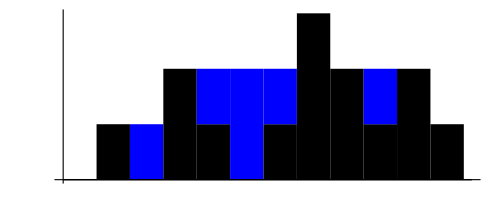

```mathematica
PlotWater[heights]
```

```mathematica
Water[heights]
```

6